First we define our system of equations and also partition a piece for solutions of a truncated system

```mathematica
alp = Table[Symbol["a" <> ToString@i],{i,1,12}];
bet = Table[Symbol["b" <> ToString@i],{i,1,12}];
alp2 = Delete[alp,{{7},{12}}];
bet2 = Delete[bet,{7}];
ns = Table[Symbol["n" <> ToString@i],{i,1,12}];
diffs = Flatten[
{Table[-Abs@alp[[i]]*ns[[i]][t],{i,1,1}],(*Uncoupled stuff*)
-(Abs@alp[[11]]+Abs@alp[[2]])*ns[[2]][t] +Abs@bet[[2]]*ns[[Length@ns]][t] + Abs@alp[[1]]*ns[[1]][t],
Table[ Abs@bet[[i]]*ns[[Length[ns]]][t] - Abs@alp[[i]]*ns[[i]][t],{i,3,10}],(*To serum stuff*)
Abs@alp[[Length[alp]-1]]* ns[[2]][t],(*Waste stuff*)
Sum[Abs@alp[[i]]*ns[[i]][t], {i,2,10}] - Sum[Abs@bet[[i]],{i,2,10}]*ns[[Length[ns]]][t]}];(*my man the serum*)
derv = Table[ns[[i]]'[t],{i,1,12}];
derv2 = Delete[derv,{7}];
system = Table[derv[[i]] == diffs[[i]],{i,1,Length[derv]}];
ns2 = Delete[ns,{7}];
diffs2 = Flatten[
{-alp2[[1]]*ns2[[1]][t],
alp2[[1]]*ns2[[1]][t] - alp2[[Length@ns2-1]]*ns2[[2]][t] + alp2[[2]]*(ns2[[2]][t] +0),
Table[
alp2[[i]]*(ns2[[i]][t]+0),{i,3,9}],
alp2[[Length@ns2-1]]*ns2[[2]][t],
Sum[-alp2[[i]]*ns2[[i]][t],{i,2,9}]}];
system2 = Table[derv2[[i]] == diffs2[[i]],{i,1,Length[derv2]}];
Length@diffs2;
{system//TableForm,approxsystem//TableForm};
{system2//TableForm,approxsystem2//TableForm}
```

{n1'[t]==-a1 n1[t]
n2'[t]==a1 n1[t]-a11 n2[t]+a2 n2[t]
n3'[t]==a3 n3[t]
n4'[t]==a4 n4[t]
n5'[t]==a5 n5[t]
n6'[t]==a6 n6[t]
n8'[t]==a8 n8[t]
n9'[t]==a9 n9[t]
n10'[t]==a10 n10[t]
n11'[t]==a11 n2[t]
n12'[t]==-a10 n10[t]-a2 n2[t]-a3 n3[t]-a4 n4[t]-a5 n5[t]-a6 n6[t]-a8 n8[t]-a9 n9[t],n1'[t]==-Abs[a1] n1[t]
n2'[t]==Abs[a1] n1[t]+Abs[b2] n12[t]+(-Abs[a11]-Abs[a2]) n2[t]
n3'[t]==Abs[b3] n12[t]-Abs[a3] n3[t]
n4'[t]==Abs[b4] n12[t]-Abs[a4] n4[t]
n5'[t]==Abs[b5] n12[t]-Abs[a5] n5[t]
n6'[t]==Abs[b6] n12[t]-Abs[a6] n6[t]
n8'[t]==Abs[b8] n12[t]-Abs[a8] n8[t]
n9'[t]==Abs[b9] n12[t]-Abs[a9] n9[t]
n10'[t]==-Abs[a10] n10[t]+Abs[b10] n12[t]
n11'[t]==Abs[a11] n2[t]
n12'[t]==0}

```mathematica
approxsystem2
```

{n1'[t]==-Abs[a1] n1[t],n2'[t]==Abs[a1] n1[t]+Abs[b2] n12[t]+(-Abs[a11]-Abs[a2]) n2[t],n3'[t]==Abs[b3] n12[t]-Abs[a3] n3[t],n4'[t]==Abs[b4] n12[t]-Abs[a4] n4[t],n5'[t]==Abs[b5] n12[t]-Abs[a5] n5[t],n6'[t]==Abs[b6] n12[t]-Abs[a6] n6[t],n8'[t]==Abs[b8] n12[t]-Abs[a8] n8[t],n9'[t]==Abs[b9] n12[t]-Abs[a9] n9[t],n10'[t]==-Abs[a10] n10[t]+Abs[b10] n12[t],n11'[t]==Abs[a11] n2[t],n12'[t]==0}

```mathematica
system2//TableForm
```

n1'[t]==a1 n1[t]
n2'[t]==a1 n1[t]+a2 (0.+n12[t])-a11 n2[t]
n3'[t]==a3 (-n12[t]+n3[t])
n4'[t]==a4 (-n12[t]+n4[t])
n5'[t]==a5 (-n12[t]+n5[t])
n6'[t]==a6 (-n12[t]+n6[t])
n8'[t]==a8 (-n12[t]+n8[t])
n9'[t]==a9 (-n12[t]+n9[t])
n10'[t]==a10 (n10[t]-n12[t])
n11'[t]==a11 n2[t]
n12'[t]==a10 n10[t]+a2 n2[t]+a3 n3[t]+a4 n4[t]+a5 n5[t]+a6 n6[t]+a8 n8[t]+a9 n9[t]

```mathematica
alp2
```

{a1,a2,a3,a4,a5,a6,a8,a9,a10,a11}

Now we prepare vectors of initial conditions as well as their counterparts.

```mathematica
initcond = {11.233753496899364,7.836250157862164,9.608970201701684,9.53240652539371,
4.357914923821371,7.7605185248645085,11.597172303950263,8.516102143592978,9.42422531532899,
5.790466859094781,0,6.856809541483823};
initcond2 = Delete[initcond,{7}];
ic = Table[ns[[i]][0] ==initcond[[i]],{i,1,Length@initcond}]
ic2 = Table[ns2[[i]][0]==initcond2[[i]],{i,1,Length@initcond2}]
points = Range[0.001,12,.3]; (*points to fit with*)
```

{n1[0]==11.2338,n2[0]==7.83625,n3[0]==9.60897,n4[0]==9.53241,n5[0]==4.35791,n6[0]==7.76052,n7[0]==11.5972,n8[0]==8.5161,n9[0]==9.42423,n10[0]==5.79047,n11[0]==0,n12[0]==6.85681}

{n1[0]==11.2338,n2[0]==7.83625,n3[0]==9.60897,n4[0]==9.53241,n5[0]==4.35791,n6[0]==7.76052,n8[0]==8.5161,n9[0]==9.42423,n10[0]==5.79047,n11[0]==0,n12[0]==6.85681}

```mathematica
{n1[0]==11.233753496899364,n2[0]==7.836250157862164,n3[0]==9.608970201701684,n4[0]==9.53240652539371,n5[0]==4.357914923821371,n6[0]==7.7605185248645085,n8[0]==8.516102143592978,n9[0]==9.42422531532899,n10[0]==5.790466859094781,n11[0]==0,n1 2[0]==6.856809541483823}
```

```mathematica
sol = ParametricNDSolveValue[
Riffle[system,ic],
Table[ns[[i]],{i,1,12}],
{t,0,15},
Flatten[{
Table[alp[[i]],{i,1,11}],
Table[bet[[i]],{i,2,10}]
}],
Method->"LSODA"]; (*set up equations to optimize*)

sol2 = ParametricNDSolveValue[
Riffle[system2,ic2],
Table[ns2[[i]],{i,1,11}],
{t,0,15},
alp2,
Method->"LSODA"]; (*set up equations to optimize*)



apsol2 =  ParametricNDSolveValue[
Riffle[approxsystem2,ic2],
Table[ns2[[i]],{i,1,11}],
{t,0,15},
params2,
Method->"LSODA"]; (*set up equations to optimize*)
```

```mathematica
points = Range[0.001,12,.3];
ordinates=With[{a1=0.12512044723935,a2=0.2453021,a3=0.7491892366497901,a4=0.44118386223923545,a5=0.17193008586682357,a6=0.922720059201386,a7=0.7124062074680186,a8=0.5898966317547063,a9 = 0.8498145306514904, a10 =0.7778254794939592,a11=0.007256062876177221,b2=0.240343, b3=0.7902230762443223,b4=0.31166228728883012,b5=0.06655575840953443,b6=0.9795814487355847,b7=0.6580558294204786,b8=0.599771396211936,b9=0.6398638788598377,b10=0.8907779882884594}
,Through[sol[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,b2,b3,b4,b5,b6,b7,b8,b9,b10][points],List]];
ordinates = Delete[ordinates,{7}];
data = ordinates+RandomVariate[NormalDistribution[0,.25],Dimensions[ordinates]];
transformedData={ConstantArray[Range@Length[ordinates],Length[points]]//Transpose,ConstantArray[points,Length[ordinates]],data}~Flatten~{{2,3},{1}};
lessData = DeleteCases[transformedData,{Length@ns2 - 1,__}];
```

```mathematica
other = Abs[initcond + RandomVariate[NormalDistribution[0,.25],Dimensions[initcond]]]
```

{11.1851,8.14909,9.82407,9.74714,4.30441,7.34262,11.8429,8.54667,9.60108,5.8004,0.257514,6.81668}

```mathematica
DataRandomSampler[regions_,equations_,nump_]:= 
(*Grab random elements from the data, sort and partition it correctly for use in the model fititng*)
Table[
Sort[
RandomSample[
Partition[regions,Length[regions]/equations][[i]],nump],
#1[[2]]<#2[[2]]&],
{i,1,equations}]~Flatten~{1,2}


EqualDataRandomSample[regions_,equations_,nump_]:= 
(*Need to have evenly spaced data, sampled randomly, which apparently is way easier to do than I thought before*)
SortBy[
RandomSample[
Transpose[Partition[regions,Length[regions]/equations]],nump]~Flatten~{1,2}, First]
ChooseData[regions_,equations_,nump_]:= 
SortBy[
Transpose[Partition[regions,Length[regions]/equations]][[nump]]~Flatten~{1,2}, First]

ModelSys[args_][i_,t_]:=Through[(sol@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

ApModelSys[args_][i_,t_]:=Through[(apsol@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

ModelSys2[args_][i_,t_]:=Through[(sol2@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

ApModelSys2[args_][i_,t_]:=Through[(apsol2@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

params = Flatten[{Table[alp[[i]],{i,1,11}],Table[bet[[i]],{i,2,10}]}];
params2 = Delete[params,{{7},{17}}];

guess = Riffle[alp2,Table[RandomReal[{-.2,.2}],{i,1,Length@alp2}]]~Partition~2
```

{{a1,-0.184392},{a2,0.0986004},{a3,0.190404},{a4,0.0487668},{a5,-0.000680533},{a6,-0.145782},{a8,0.0810207},{a9,-0.133613},{a10,-0.0684242},{a11,-0.118331}}

```mathematica
guess={{a1,0.15505974866889738},{a2,0.004959099999999994},{a3,0.04103383959453222},{a4,-0.12186738888225856},{a5,-0.10537432745728914},{a6,0.056616236429147374},{a8,0.01002017108935412},{a9,-0.20390550089323555},{a10,0.11437742310177825},{a11,0.0056417214273246974}}
```

{{a1,0.15506},{a2,0.0049591},{a3,0.0410338},{a4,-0.121867},{a5,-0.105374},{a6,0.0566162},{a8,0.0100202},{a9,-0.203906},{a10,0.114377},{a11,0.00564172}}

```mathematica
guess
```

{{a1,0.0441334},{a2,0.0623465},{a3,0.0813149},{a4,0.0528161},{a5,0.0114599},{a6,0.0120268},{a8,0.0107936},{a9,0.0255959},{a10,0.0732603},{a11,0.0986283}}

```mathematica
fitdata =ChooseData[transformedData,Length@ns2,{2,6,10,30}];(*EqualDataRandomSample[lessData,Length@ns-1,4];*)
fit3=NonlinearModelFit[fitdata,
ModelSys2[alp2][i,t],
guess,{i,t},
Method->"LevenbergMarquardt",
PrecisionGoal->∞,
MaxIterations->600];
```

```mathematica
fit3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 0.13575 | 0.0206982 | 6.55853 | 1.63615×10^-7
a2 | -0.0508275 | 0.0146004 | -3.48125 | 0.00139075
a3 | 0.00264674 | 0.0095064 | 0.278417 | 0.782379
a4 | -0.0583133 | 0.0152128 | -3.83318 | 0.000520914
a5 | -0.0296429 | 0.0269756 | -1.09888 | 0.279543
a6 | 0.0344538 | 0.0090734 | 3.79723 | 0.000576678
a8 | 0.00867237 | 0.0102181 | 0.848724 | 0.401971
a9 | -0.0451894 | 0.0140045 | -3.22679 | 0.00276926
a10 | 0.0789354 | 0.00834494 | 9.45908 | 4.7514×10^-11
a11 | -0.000939069 | 0.00913937 | -0.10275 | 0.918765

```mathematica
replacerules =Table[fit3["BestFitParameters"][[i,2]],{i,1,Length@fit3["BestFitParameters"]}];
(*upper = Table[fit3["ParameterConfidenceIntervals"][[i,1]],{i,1,Length@fit2["BestFitParameters"]}];
lower =  Table[fit3["ParameterConfidenceIntervals"][[i,2]],{i,1,Length@fit2["BestFitParameters"]}];*)
replace = Table[alp2[[i]] -> replacerules[[i]],{i,1,Length@alp2}];
(*upreplace = Table[params[[i]]-> upper[[i]],{i,1,Length@params}];
lowreplace = Table[params[[i]]-> lower[[i]],{i,1,Length@params}];*)
fitsolution=NDSolve[Flatten@{system2/.replace, ic2},ns2,{t,0,10}];
```

```mathematica
Flatten@{system2/.replace}
```

{n1'[t]==0.162489 n1[t],n2'[t]==7.83625-0.162489 n1[t]+1.31804 n12[t]-0.111426 n2[t],n3'[t]==9.60897-0.409345 n12[t],n4'[t]==9.53241-0.444001 n12[t],n5'[t]==4.35791+0.255255 n12[t],n6'[t]==7.76052-0.143068 n12[t],n8'[t]==8.5161-0.26244 n12[t],n9'[t]==9.42423-0.420599 n12[t],n10'[t]==5.79047+0.111426 n12[t],n11'[t]==0.111426 n2[t],n12'[t]==0.00526916 n10[t]}

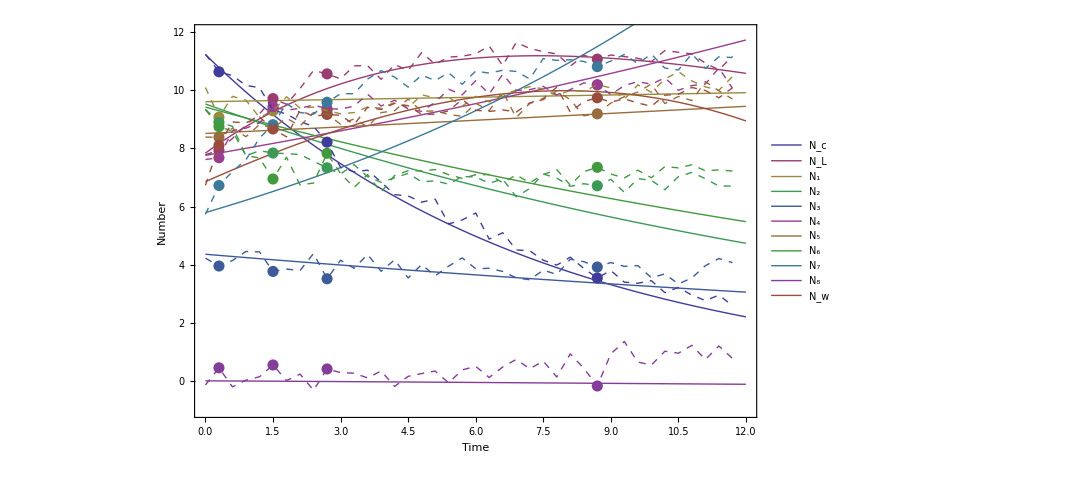

```mathematica
Show[Plot[Evaluate[Through[ns2[t]]/.fitsolution],{t,0,12},PlotStyle -> Thick,PlotLegends->legend],
(*Plot[Evaluate[Through[ns[t]]/.minussol],{t,0,10},PlotStyle -> Thick],
Plot[Evaluate[Through[ns[t]]/.plussol],{t,0,10},PlotStyle -> Thick],*)
ListPlot[Partition[Take[fitdata,All,{2,3}],4],DataRange->{0,10},
PlotRange-> All,AxesOrigin-> {0,0},PlotStyle->{AbsolutePointSize[8]}],
ListLinePlot[Take[transformedData,All,{2,3}]~Partition~Length@data[[1]],DataRange->{0,10},PlotRange-> All,AxesOrigin-> {0,0},PlotStyle->Dashed],PlotRange->{-1,12},AxesOrigin->{0,0},ImageSize-> 800,Frame->True,FrameLabel-> {Style["Time",FontSize->18],Style["Number",FontSize->18]},PlotRangePadding->0,FrameTicksStyle->Directive[FontSize->16]]
```

```mathematica
listgrabs = {{2,4,8,30},{2,4,6,8,30},{2,4,6,8,12,14,30},{2,4,6,8,12,14,16,30}}
ParamEstimates =Table[{},{j,1,Length@listgrabs}]
points = Range[0.001,12,.3];
ic = Table[ns[[i]][0] ==initcond[[i]],{i,1,Length@initcond}];
sol = ParametricNDSolveValue[
Riffle[system,ic],
Table[ns[[i]],{i,1,12}],
{t,0,15},
Flatten[{
Table[alp[[i]],{i,1,11}],
Table[bet[[i]],{i,2,10}]
}],
Method->"LSODA"]; (*set up equations to optimize*)
Quiet@
Do[
count = 1;
dump = {};
While[count<501,
(*Now we have to redefine our system every time*)
other = Abs[Delete[initcond,{7}] + RandomVariate[NormalDistribution[0,.25],Dimensions[Delete[initcond,{7}]]]];
diffs2 = Flatten[
{-alp2[[1]]*ns2[[1]][t],
alp2[[1]]*ns2[[1]][t] - alp2[[Length@ns2-1]]*ns2[[2]][t] + alp2[[2]]*(ns2[[Length@ns2]][t] + other[[2]]),
Table[
alp2[[i]]*(ns2[[Length@ns2]][t]+other[[i]]),{i,3,9}],
alp2[[Length@ns2-1]]*ns2[[2]][t],
Sum[alp2[[i]],{i,2,9}]*ns2[[Length@ns2-2]][t]}]
system2 = Table[derv2[[i]] == diffs2[[i]],{i,1,Length[derv2]}];
Length@diffs2

 (*Also add noise to the inital conditions of the parameters*)
ic2 = Table[ns2[[i]][0]==other[[i]],{i,1,Length@other}];

sol2 = ParametricNDSolveValue[
Riffle[system2,ic2],
Table[ns2[[i]],{i,1,11}],
{t,0,15},
alp2,
Method->"LSODA"]; (*set up equations to optimize*)


ordinates=With[{a1=0.12512044723935,
a2=0.2453021,
a3=0.7491892366497901,
a4=0.44118386223923545,
a5=0.17193008586682357,
a6=0.922720059201386,
a7=0.7124062074680186,
a8=0.5898966317547063,
a9 = 0.8498145306514904,
 a10 =0.7778254794939592,
a11=0.007256062876177221,
b2=0.240343, 
b3=0.7902230762443223,
b4=0.31166228728883012,
b5=0.06655575840953443,
b6=0.9795814487355847,
b7=0.6580558294204786,
b8=0.599771396211936,
b9=0.6398638788598377,
b10=0.8907779882884594}
,Through[sol[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,b2,b3,b4,b5,b6,b7,b8,b9,b10][points],List]
];

ordinates = Delete[ordinates,{7}]; (*get rid of data set we're pretending we don't know about*)
data = ordinates+RandomVariate[NormalDistribution[0,.25],Dimensions[ordinates]];

transformedData={ConstantArray[Range@Length[ordinates],Length[points]]//Transpose,ConstantArray[points,Length[ordinates]],data}~Flatten~{{2,3},{1}};
lessData = DeleteCases[transformedData,{Length@ns2 - 1,__}];

fitdata =ChooseData[lessData,Length@ns2-1,listgrabs[[k]]];

guess = Riffle[alp2,Table[RandomReal[{0,.1}],{i,1,Length@alp2}]]~Partition~2;

fit3=NonlinearModelFit[fitdata,
ModelSys2[alp2][i,t],
guess,{i,t},
Method->"LevenbergMarquardt",
PrecisionGoal->∞,
MaxIterations->600];

AppendTo[ParamEstimates[[k]],Table[fit3["BestFitParameters"][[i,2]],{i,1,Length@alp2}]];
count++
];
Print[k];
,{k,1,Length@listgrabs}]
```

{{2,4,8,30},{2,4,6,8,30},{2,4,6,8,12,14,30},{2,4,6,8,12,14,16,30}}

{{},{},{},{}}

1

2

3

4

```mathematica
Filter[array_]:=
Table[
If[
array[[i]] > Mean[array] +  2*StandardDeviation[array],
{i},
Unevaluated[Sequence[]]],
{i,1,Length@array}];
size[array1_,array2_]:=
If[Length@array1 == Length@array2,
Unevaluated[Sequence[]],
If[Length@array1 > Length@array2,
Return[Delete[array2,Table[{i},{i,Length@array1,Length@array2}]]],
Return[Delete[array1,Table[{i},{i,Length@array2,Length@array1}]]]
]
]
size[array1_,array2_]:=
If[Length@array1 == Length@array2,
Unevaluated[Sequence[]],
If[Length@array1 > Length@array2,
Return[Delete[array2,Table[{i},{i,Length@array1,Length@array2}]]],
Return[Delete[array1,Table[{i},{i,Length@array2,Length@array1}]]]
]
]
Needs["MultivariateStatistics`"]
Plotter[array1_,array2_,label1_,label2_]:= 
Show[
ListPlot[Transpose@{array1,array2}],
Graphics[{Thick,Red,Opacity[.4],EllipsoidQuantile[Transpose@{array1,array2},.95]}],
Graphics[{
Style[Text["α =",Scaled[{0.1,0.9}]],FontSize->16],
Style[Text[ToString@Round[Mean[array1],10.^-3],Scaled[{0.2,0.9}]],FontSize->16],
Style[Text["±",Scaled[{0.3,0.9}]],FontSize->16],
Style[Text[ToString[Round[2*StandardDeviation[array1],10.^-3]],Scaled[{0.4,0.9}]],FontSize->16]
}],
Graphics[{
Style[Text["β =",Scaled[{0.1,0.8}]],FontSize->16],
Style[Text[ToString@Round[Mean[array2],10.^-3],Scaled[{0.2,0.8}]],FontSize->16],
Style[Text["±",Scaled[{0.3,0.8}]],FontSize->16],
Style[Text[ToString[Round[2*StandardDeviation[array2],10.^-3]],Scaled[{0.4,0.8}]],FontSize->16]
}],
Frame -> True, FrameLabel ->{Style[label1,FontSize->18],Style[label2,FontSize->18]},ImageSize-> 400,PlotRange-> All,Axes-> False,FrameTicksStyle->Directive[FontSize->17]];
```

```mathematica
axes = {Subscript[α, c],Subscript[α, L],Subscript[α, 1],Subscript[α, 2],Subscript[α, 3],Subscript[α, 4],Subscript[α, 5],Subscript[α, 6],Subscript[α, 7],Subscript[α, 8]};
```

```mathematica
Listplots=Table[{},{i,1,Length@listgrabs}]
Do[
estimates =Transpose@ParamEstimates[[i]];
Do[
fxpoints =estimates[[j]];
AppendTo[Listplots[[i]],Histogram[fxpoints,{"Raw",25},ImageSize-> 400]],
{j,1,9}]
,{i,1,Length@listgrabs}]
```

{{},{},{},{}}

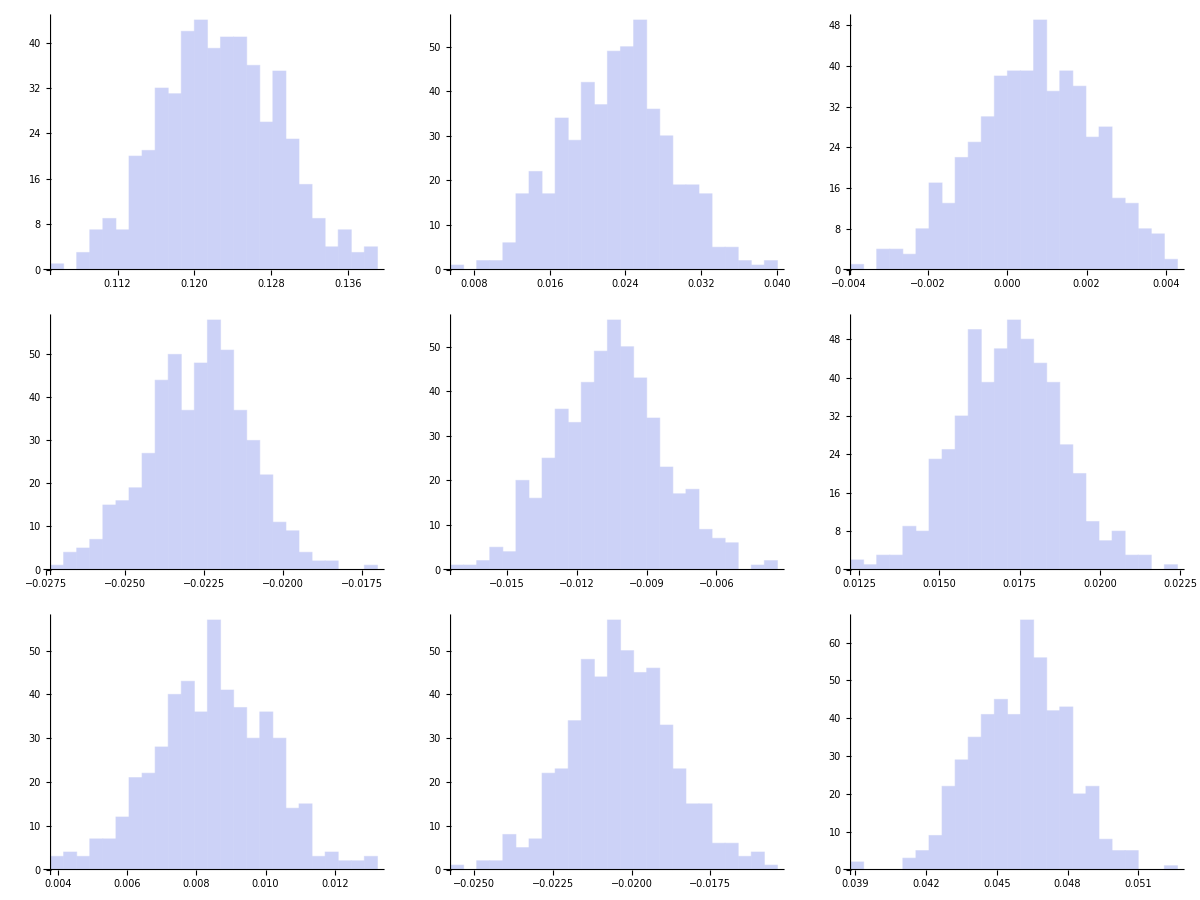

```mathematica
save =Grid[Listplots[[2]]~Partition~3]
```

```mathematica
Export["BS27.pdf",save]
```

BS27.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["BS27.pdf"]]]
```

```mathematica
alp2
```

{a1,a2,a3,a4,a5,a6,a8,a9,a10,a11}